```mathematica
Subsystems[vectorField_List,stateVars_List]:=Module[{
Jac=Map[Grad[#,stateVars]&, vectorField]
},
(* Compute the adjacency matrix for the system  *)
AdjMat=Map[If[TrueQ[Simplify[#==0]],0,1]&,Jac, {2}];
(* Compute the adjacency graph from the matrix *)
AdjGraph=AdjacencyGraph[stateVars,AdjMat, VertexLabels->"Name"];
(* Compute the weakly connected components in the adjacency graph *)
SubComponents=WeaklyConnectedComponents[AdjGraph];
(* Construct the independent sub-systems *)
{Map[ #.vectorField &,Map[Grad[#,stateVars]&,SubComponents]], SubComponents}//Transpose
]

DependencySystems[vectorField_List,stateVars_List]:=Module[{
Jac=Map[Grad[#,stateVars]&, vectorField]
},
(* Compute the adjacency matrix for the system  *)
AdjMat=Map[If[TrueQ[Simplify[#==0]],0,1]&,Jac, {2}];
(* Compute the adjacency graph from the matrix *)
AdjGraph=AdjacencyGraph[stateVars,AdjMat//Transpose, VertexLabels->"Name"]
(* Compute the weakly connected components in the adjacency graph *)
(* SubComponents=WeaklyConnectedComponents[AdjGraph], *)
(* Construct the independent sub-systems *)
(*{Map[ #.vectorField &,Map[Grad[#,stateVars]&,SubComponents]], SubComponents}//Transpose *)
]
```

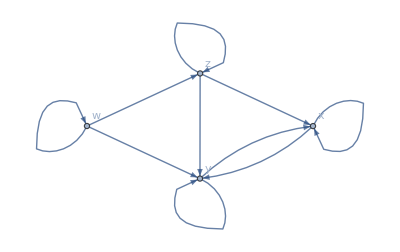

```mathematica
dependsys=DependencySystems[vf,vars]
```

```mathematica
Map[Length[VertexOutComponent[dependsys,#]]&, vars]
SortBy[vars,Length[VertexOutComponent[dependsys,#]]&]
```

{2,2,4,3}

{x,y,z,w}

```mathematica
Sort[{DegreeCentrality[dependsys, "Out"],vars}//Transpose]
```

{{1,x},{1,y},{2,w},{2,z}}

```mathematica
PrettyPrint[f_List,var_List]:=Module[{},
{Map[ToString[#]<>"'="&,var],f}//Transpose//MatrixForm
]

vf={x^6*y*y-z+y*y,w*z*y+x+22,w,z*w};
vars={x,y,w,z};
PrettyPrint[vf,vars]
```

(x'= | y^2+x^6 y^2-z
y'= | 22+x+w y z
w'= | w
z'= | w z)

```mathematica
subsys=Subsystems[vf,vars];
dependsys=DependencySystems[vf,vars];
Map[PrettyPrint[#//First,#//Last] &, subsys]
Map[PrettyPrint[#//First,#//Last] &, dependsys]
```

{(w'= | w
z'= | w z),(x'= | -1+x^6 y+y^2
y'= | 22+x+y)}

{(w'= | w
z'= | w z),(x'= | -1+x^6 y+y^2
y'= | 22+x+y)}

```mathematica
ProductProblems[problem_List]:=Module[{Project},
{precond,{vectorfield,statevars,constraint}, postcond}=problem;
unsafe=Not[postcond];
Project[S_,elimvars_List,projvars_List]:=Resolve[Exists[elimvars,S],Reals];
Map[{
Project[precond,Complement[statevars,Last[#]],Last[#]],
{First[#],Last[#],Project[constraint,Complement[statevars,Last[#]],Last[#]]} ,
Not[Project[unsafe,Complement[statevars,Last[#]],Last[#]]]//Simplify
}&, Subsystems[vectorfield,statevars]]
]
```

```mathematica
xinit=(x-1)^2+(y+3)^2≤1;
safe=(x+3)^2+(y-2)^2>=3;
problem={xinit,{{x,-y},{x,y},x^2+y^2≤1000},safe};
ProductProblems[problem]//MatrixForm
```

(-4≤y≤-2 | {{-y},{y},-10 √10≤y≤10 √10} | y≥2+√3||√3+y≤2
0≤x≤2 | {{x},{x},-10 √10≤x≤10 √10} | 3+x≥√3||3+√3+x≤0)

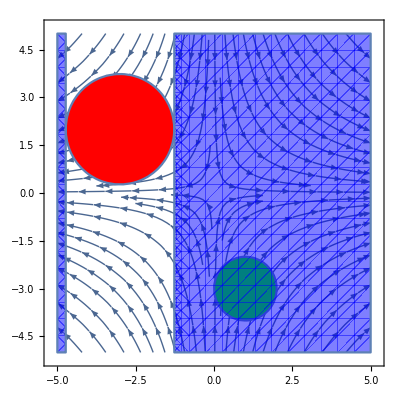

```mathematica
Show[
StreamPlot[problem[[2]]//First, {x,-5,5},{y,-5,5}],
RegionPlot[problem//First,{x,-5,5},{y,-5,5},PlotStyle->Green],
RegionPlot[Not[problem//Last],{x,-5,5},{y,-5,5},PlotStyle->Red],
RegionPlot[3+x≥√3||3+√3+x≤0,{x,-5,5},{y,-5,5},PlotStyle->Directive[Blue,Opacity[0.5]]]
]
```